```mathematica
ClearAll["Global`*"]
```

```mathematica
norm[θ_]:=θ-2π Floor[θ/(2π)]
```

```mathematica
n=127;
```

```mathematica
(*check ys*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/fluid_structure_interaction/fluid_obstacle/remesh/solution/snapshots/csv/ys_test_" <>ToString[n]<>".csv"][[2;;]];
t=Table[{t[[i,3]],t[[i,1]],t[[i,2]]},{i,2,Length[t]}]
```

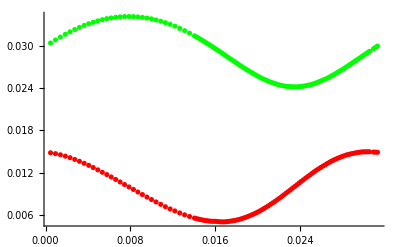

```mathematica
Show[ListPlot[Table[{t[[i,1]],t[[i,2]]},{i,1,Length[t]}],PlotStyle->Red],ListPlot[Table[{t[[i,1]],t[[i,3]]},{i,1,Length[t]}],PlotStyle->Green],PlotRange->Full]
```

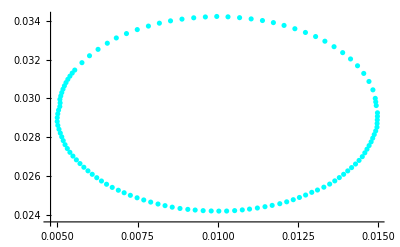

```mathematica
ListPlot[Table[{t[[i,2]],t[[i,3]]},{i,1,Length[t]}],PlotStyle->Cyan]
```

```mathematica
(*check U*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/fluid_structure_interaction/fluid_obstacle/remesh/solution/snapshots/csv/U_n_12_sm_" <>ToString[n]<>".csv"][[2;;]];
t=Table[{t[[i,3]],t[[i,1]],t[[i,2]]},{i,2,Length[t]}]
```

```mathematica
Min[Table[t[[i,2]],{i,1,Length[t]}]]
Max[Table[t[[i,2]],{i,1,Length[t]}]]
Min[Table[t[[i,3]],{i,1,Length[t]}]]
Max[Table[t[[i,3]],{i,1,Length[t]}]]
```

0.

0.

0.

«1 more identical outputs»

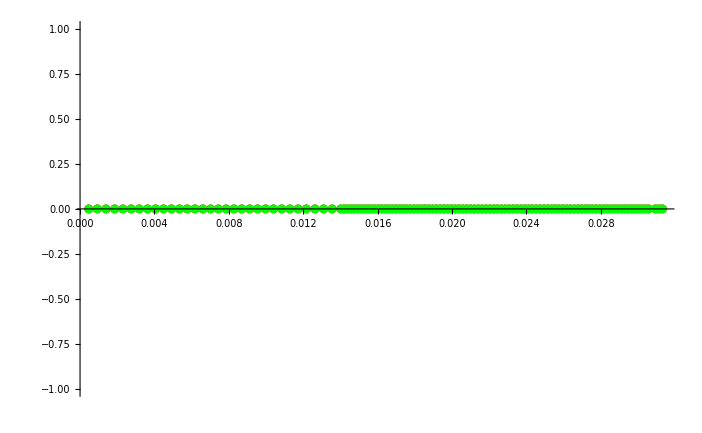

```mathematica
Show[ListPlot[Table[{t[[i,1]],t[[i,2]]},{i,1,Length[t]}],PlotStyle->Red],ListPlot[Table[{t[[i,1]],t[[i,3]]},{i,1,Length[t]}],PlotStyle->Green],PlotRange->Full]
```

```mathematica
(*check nu*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/fluid_structure_interaction/fluid_obstacle/remesh/solution/snapshots/csv/nu_n_12_" <>ToString[n]<>".csv"][[2;;]];
t=Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

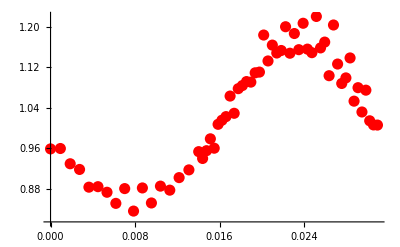

```mathematica
plotnumν=ListPlot[t,PlotStyle->{Red,PointSize->0.02}]
```

```mathematica
(*check psi*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/fluid_structure_interaction/fluid_obstacle/remesh/solution/snapshots/csv/dpsi_n_12_" <>ToString[n]<>".csv"][[2;;]];
t=Table[{t[[i,2]],norm[t[[i,1]]]},{i,2,Length[t]}]
```

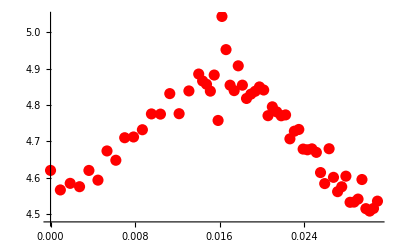

```mathematica
plotnumψ=ListPlot[t,PlotStyle->{Red,PointSize->0.02}]
```

```mathematica
(*check mu*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/fluid_structure_interaction/fluid_obstacle/remesh/solution/snapshots/csv/mu_n_12_" <>ToString[n]<>".csv"][[2;;]];
t=Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

{{0.0185456,133.792},{0.0201707,146.017},{0.0177626,53.8782},{0.0209884,73.7843},{0.0169915,227.7},{0.0218298,102.121},{0.0162218,-55.599},{0.0226523,100.547},{0.0154888,154.337},{0.0234941,113.624},{0.0147603,113.355},{0.0243121,70.4777},{0.0140212,87.0064},{0.0251548,149.731},{0.0121672,109.655},{0.0259446,23.1216},{0.0104005,98.7368},{0.0267762,180.922},{0.008692,98.5983},{0.0275557,33.0364},{0.00701727,99.8362},{0.0283455,170.642},{0.00534342,95.9243},{0.0290989,16.2769},{0.00363205,103.617},{0.0298413,190.3},{0.00185964,109.433},{0.0305645,42.5493},{0.0313103,91.6025}}

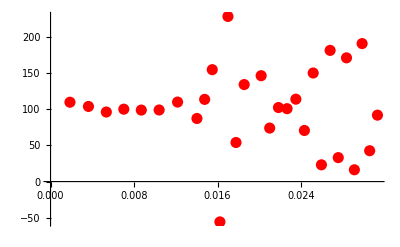

```mathematica
plotnumμ=ListPlot[t,PlotStyle->{Red,PointSize->0.02}]
```